```mathematica
file="/Users/vpk/Google\ Drive/Jlab/Projects/Mathematica/densities.txt";
Hdata=ReadList[file,{Number,Number,Number,Number,Number}];
X=Hdata[[All,1]];

HForwardu=Hdata[[All,2]];
HProfileu=Hdata[[All,3]];
HForwardd=Hdata[[All,4]];
HProfiled=Hdata[[All,5]];

xmin=1.9924×10^-5;
xmax=0.5;
ymin=0;
ymax=15;
HFu=Interpolation[Thread[{X,HForwardu}],InterpolationOrder->1];
HFd=Interpolation[Thread[{X,HForwardd}],InterpolationOrder->1];
HPu=Interpolation[Thread[{X,HProfileu}],InterpolationOrder->1];
HPd=Interpolation[Thread[{X,HProfiled}],InterpolationOrder->1];
Hu[x_,t_]:=HFu[x]*Exp[HPu[x]*t];
Hd[x_,t_]:=HFd[x]*Exp[HPd[x]*t];

PlotFL=Plot[{HFu[x],HFd[x]},{x,xmin,xmax},PlotRange->{{xmin,xmax},{ymin,ymax}},FrameLabel->{"x","Forward Limit"},PlotLegends->Placed[{u-quark,d-quark},Center],Frame->True,Filling->Axis,ImageSize->Medium,PlotLabel->"Forward Limit"];
PlotPF=Plot[{HPu[x],HPd[x]},{x,xmin,xmax},PlotRange->{{xmin,xmax},{ymin,ymax}},FrameLabel->{"x","Profile FUnction"},PlotLegends->Placed[{u-quark,d-quark},Center],Frame->True,Filling->Axis,ImageSize->Medium,PlotLabel->"Profile Function"];
xx=0.1;
 PlotH=Plot[{Hu[0.1,-t],Hd[0.1,-t]},{t,0,1},FrameLabel->{"-t","H(x=0.1,-t"},PlotLegends->Placed[{u-quark,d-quark},Center],Frame->True,Filling->Axis,ImageSize->Medium,PlotLabel-> "H(x=0.1,-t)"];
PlotHu=DensityPlot[Hu[x,-t],{x,0.1,0.5},{t,0,1},ColorFunction->"SunsetColors",PlotLegends->Automatic];
PlotHd=DensityPlot[Hd[x,-t],{x,0.1,0.5},{t,0,1},ColorFunction->"SunsetColors",PlotLegends->Automatic];
Au=0.5;
Bu=0.5;
αu=0.3;
αu'=0.45;
nu=4.83;
βu=4;
ETPFu[x_]:=(Bu+αu'Log[1./x])*(1.-x)^3+Au*x*(1.-x)^2;
ETFLu[x_]:=nu*x^αu*(1.-x)^βu;


Ad=0.5;
Bd=0.5;
αd=0.3;
αd'=0.45;
nd=3.57;
βd=5;
ETPFd[x_]:=(Bd+αd'Log[1./x])*(1.-x)^3+Ad*x*(1.-x)^2;
ETFLd[x_]:=nd*x^αd*(1.-x)^βd;

ETu[x_,t_]:=ETFLu[x]*Exp[ETPFu[x]*t];
ETd[x_,t_]:=ETFLd[x]*Exp[ETPFd[x]*t];

GeVFm=0.1973;

HDeNu  [x_,bx_,by_]:=1./(4*π)*HFu[x]/HPu[x]*Exp[-(bx^2+by^2)/(4*HPu[x])];
ETDeNu[x_,bx_,by_]:=1./(4*π)*ETFLu[x]/ETPFu[x]*Exp[-(bx^2+by^2)/(4*ETPFu[x])];
DeNu    [x_,bx_,by_]:=1./2.*(HDeNu[x,bx,by]+1./4.*by/(0.938*ETFLu[x])*ETDeNu[x,bx,by]);
DenXYu[x_,bx_,by_]:=DeNu[x,bx/GeVFm,by/GeVFm]*GeVFm^2;

HDeNd  [x_,bx_,by_]:=1./(4*π)*HFd[x]/HPd[x]*Exp[-(bx^2+by^2)/(4*HPd[x])];
ETDeNd[x_,bx_,by_]:=1./(4*π)*ETFLd[x]/ETPFd[x]*Exp[-(bx^2+by^2)/(4*ETPFd[x])];
DeNd    [x_,bx_,by_]:=1./2.*(HDeNd[x,bx,by]+1./4.*by/(0.938*ETFLd[x])*ETDeNd[x,bx,by]);
DenXYd[x_,bx_,by_]:=DeNd[x,bx/GeVFm,by/GeVFm]*GeVFm^2;



xd=0.42;
(*
 Print["HFu[",xd,"]=",HFu[xd]]
Print["HFd[",xd,"]=",HFd[xd]]
Print["HDeNu[0.,0.]=",HDeNu[xd,0.,0.]]
Print["DenXYu[0.,0.]=",DenXYu[xd,0.,0.]]
Print["DenXYd[0.,0.]=",DenXYd[xd,0.,0.]]
*)
```

Syntax::bktmop: Expression "*)" has no opening "(".

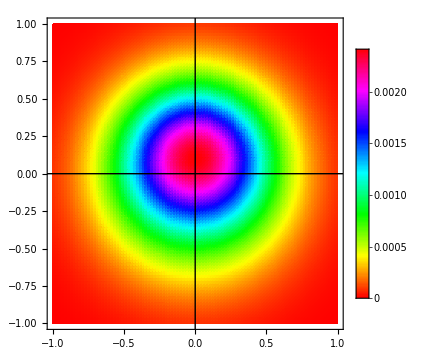
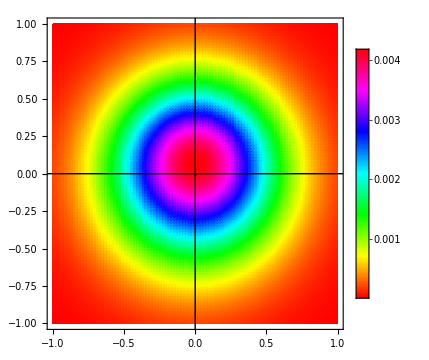

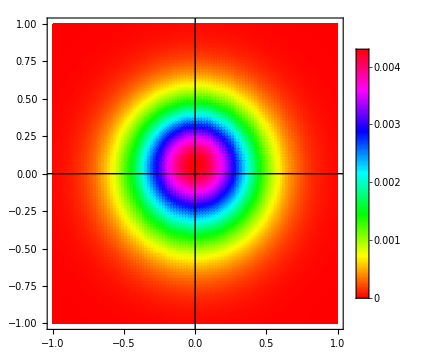
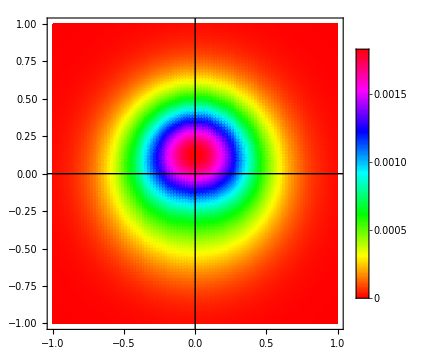

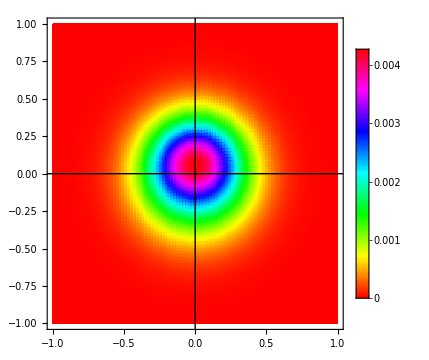
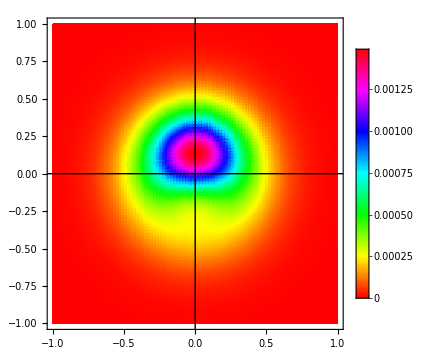

1.58824

0.0235976

0.0184697

0.45

0.0906169

0.245199

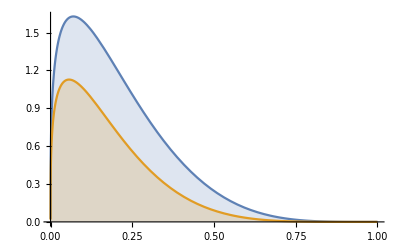

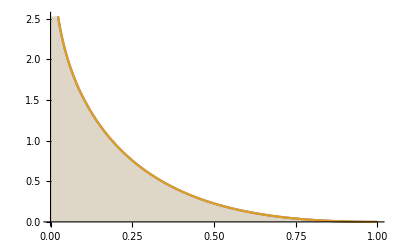

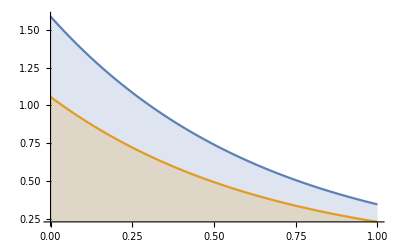

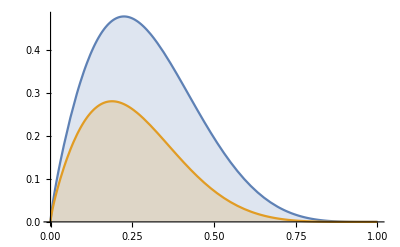

0.858571

```mathematica
xd=0.1;
HDeNu[1.,1.]
DeNu[1.,1.]
Print[ETFLu[0.1]]
DensityPlot[DeNu[bx,by],{bx,-5,5},{by,-5,5},ColorFunction->Hue,PlotLegends->Automatic]


PlotETPF=Plot[{ETPFu[xd],ETPFd[xd]},{xd,0,1},Filling->Axis];PlotETFL=Plot[{ETFLu[xd],ETFLd[xd]},{xd,0,1},Filling->Axis];
PlotETt=Plot[{ETu[0.1,-t],ETd[0.1,-t]},{t,0,1},Filling->Axis];
PlotETx=Plot[{ETu[xd,-1.0],ETd[xd,-1.0]},{xd,0,1},Filling->Axis];
PlotETFL
```

```mathematica
ETFLu[0.6] 
ETFLd[0.6]
```

0.0313627

0.0313627

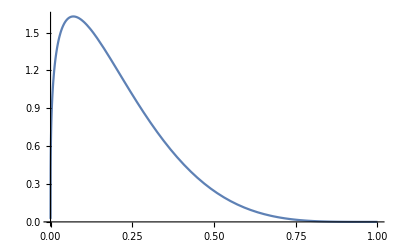

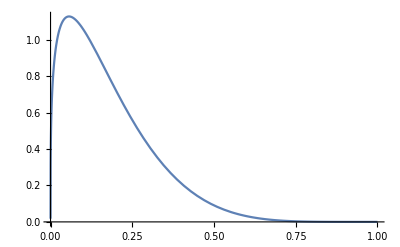

```mathematica
Plot[ETFLu[xd],{xd,0,1}]    
    Plot[ETFLd[xd],{xd,0,1}]
```

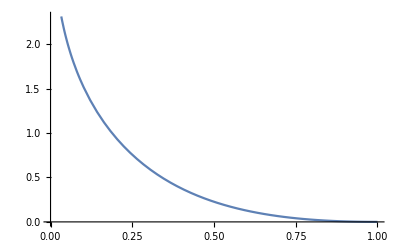

Null

```mathematica
Plot[ETPFd[x],{x,0,1}]
Exp[1.]
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

Null

Null

```mathematica
Null
```

Null

Null

Null

```mathematica
Null
```

Null

0.3

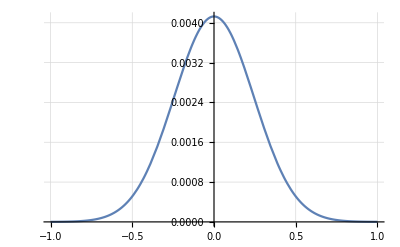

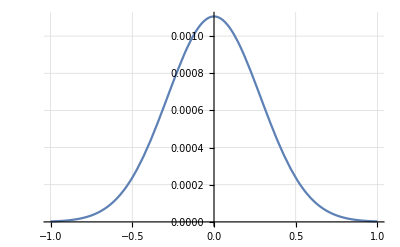

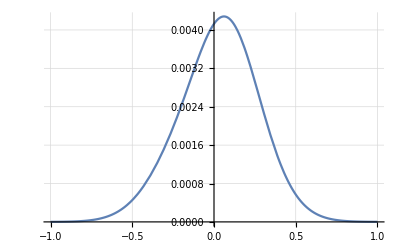

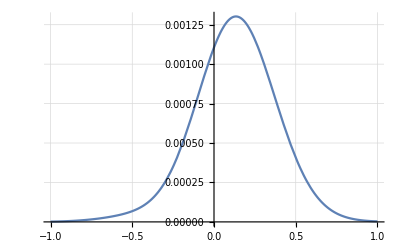

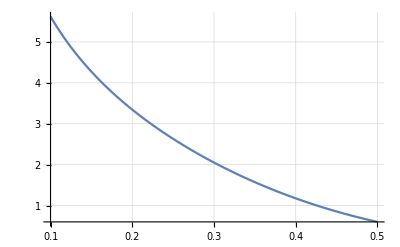

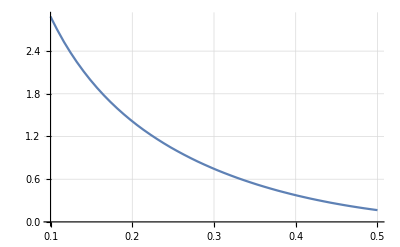

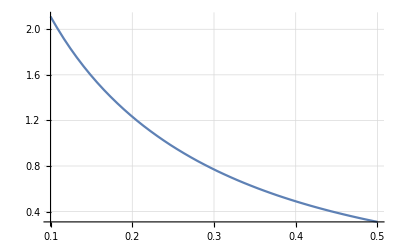

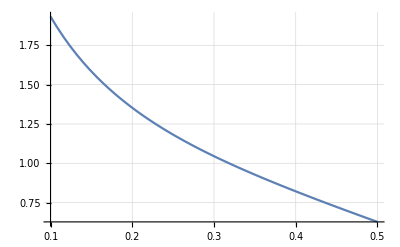

ETFL

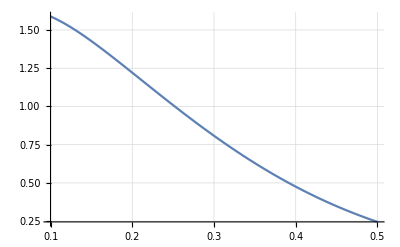

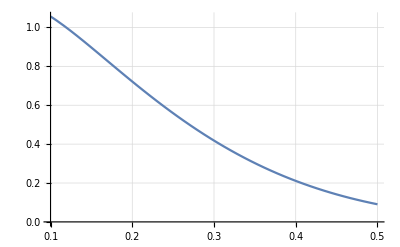

ETPF

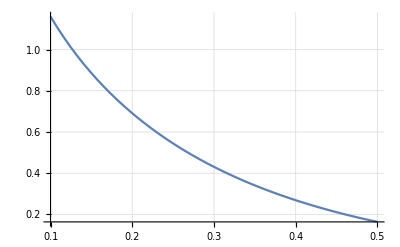

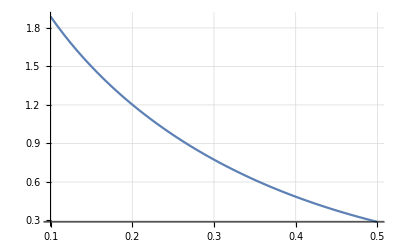

-Graphics-

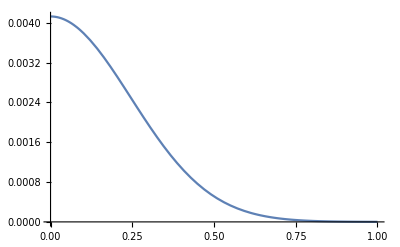

```mathematica
xd=0.3
Plot[DenXYu[x,0.],{x,-1.,1.},GridLines->Automatic]
Plot[DenXYd[x,0.],{x,-1.,1.},GridLines->Automatic]
Plot[DenXYu[0.,x],{x,-1.,1.},GridLines->Automatic]
Plot[DenXYd[0.,x],{x,-1.,1.0},GridLines->Automatic]
Plot[HFu[x],{x,0.1,0.5},GridLines->Automatic]
Plot[HFd[x],{x,0.1,0.5},GridLines->Automatic]
Plot[HPu[x],{x,0.1,0.5},GridLines->Automatic]
Plot[HPd[x],{x,0.1,0.5},GridLines->Automatic]
Print[ETFL]
Plot[ETFLu[x],{x,0.1,0.5},GridLines->Automatic]
Plot[ETFLd[x],{x,0.1,0.5},GridLines->Automatic]
Print[ETPF]

Plot[ETPFu[x],{x,0.1,0.5},GridLines->Automatic]
Plot[ETPFd[x],{x,0.1,0.5},GridLines->Automatic]

Plot[ETPFd[x],{x,0.1,0.5},GridLines->Automatic]
Plot[DenXYu[x,0.],{x,0,1}]
```

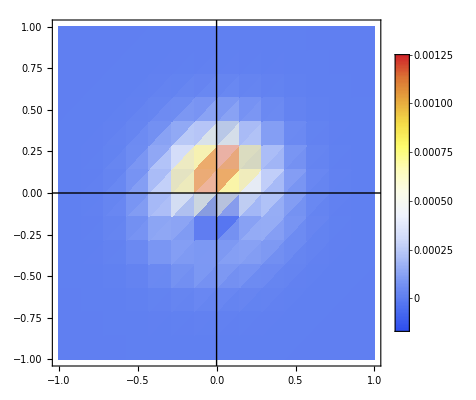

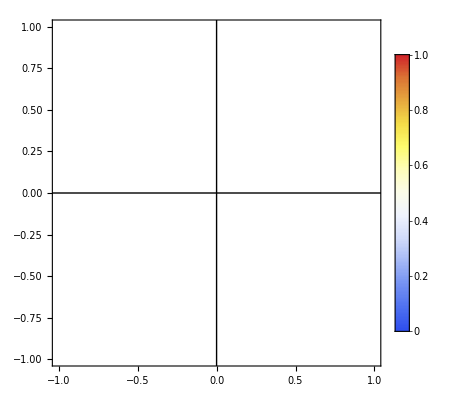

-Graphics3D-

-Graphics3D-

-Graphics3D-

«4 more identical outputs»

-Graphics3D-

```mathematica
xd=0.42;
DensityPlot[DenXYd[x,y],{x,-1,1},{y,-1,1},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->Full,Epilog->{Directive[lineStyle],line1,line2}]
DensityPlot[DenXYd,{x,-1,1},{y,-1,1},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->Full,Epilog->{Directive[lineStyle],line1,line2}]
xd=0.1;Plot3D[DenXYd[bx,by],{bx,-1,1},{by,-1,1},ColorFunction->(ColorData["TemperatureMap"][#3]&),PlotRange->All]
xd=0.2;Plot3D[DenXYd[bx,by],{bx,-1,1},{by,-1,1},ColorFunction->(ColorData["TemperatureMap"][#3]&),PlotRange->All]
xd=0.3;Plot3D[DenXYd[bx,by],{bx,-1,1},{by,-1,1},ColorFunction->(ColorData["TemperatureMap"][#3]&),PlotRange->All]
xd=0.4;Plot3D[DenXYd[bx,by],{bx,-1,1},{by,-1,1},ColorFunction->(ColorData["TemperatureMap"][#3]&),PlotRange->All]
xd=0.5;Plot3D[DenXYd[bx,by],{bx,-1,1},{by,-1,1},ColorFunction->(ColorData["TemperatureMap"][#3]&),PlotRange->All]
xd=0.6;Plot3D[DenXYd[bx,by],{bx,-1,1},{by,-1,1},ColorFunction->(ColorData["TemperatureMap"][#3]&),PlotRange->All]
xd=0.7;Plot3D[DenXYd[bx,by],{bx,-1,1},{by,-1,1},ColorFunction->(ColorData["TemperatureMap"][#3]&),PlotRange->All]
```